```mathematica
{{cSVOKp[G],cSVOKp[L],cSVOKp[P]},{cSVQEDp[G],cSVQEDp[L],cSVQEDp[P]}}=<<"~/Physik/PhD/MMa/data/ElProduction.cSV.m";
```

```mathematica
rep=Module[{vs,solβ,sols,vq,solβq,solq},
vs={ρ-> 4m2/s,β-> Sqrt[1-ρ],χ-> (1-β)/(1+β)};
solβ=Solve[χ==(χ/.vs),β][[1,1]];
sols=Solve[χ==(χ//.vs),s][[1,1]];
vq={ρq-> 4m2/q2,βq-> Sqrt[1-ρq],χq-> (βq-1)/(βq+1)};
solβq=Solve[χq==(χq/.vq),βq][[1,1]];
solq=Solve[χq==(χq//.vq),q2][[1,1]];
{sp-> s-q2,u1-> -sp-t1,t1->-sp/2(1-β ct1)/.solβ,sols,solq,solβ,solβq}
]
```

{sp→-q2+s,u1→-sp-t1,t1→-1/2 sp (1-(ct1 (1-χ))/(1+χ)),s→(m2 (1+χ)^2)/χ,q2→-(m2 (-1+χq)^2)/χq,β→(1-χ)/(1+χ),βq→(-1-χq)/(-1+χq)}

108.354-96.0555 ct1^2-10.8947 ct1^4-1.2102 ct1^6-0.193805 ct1^8

-218.648+561.049 Cos[ct1]-387.255 Cos[ct1]^2+221.584 Cos[ct1]^3-82.7084 Cos[ct1]^4+14.332 Cos[ct1]^5

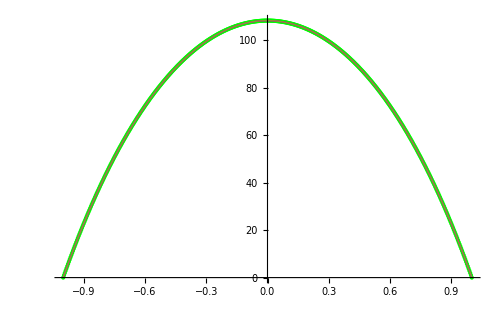
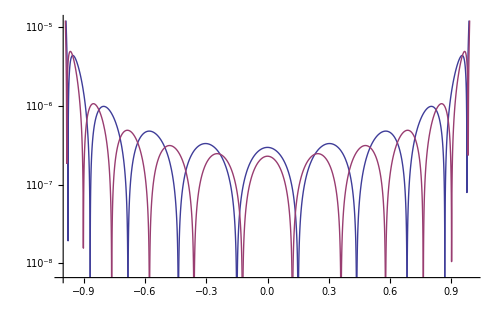

```mathematica
Module[{e,f,ff,N,xs,data,fitpol,fitcos},
e=cSVQEDp@L/.{ln[βtil]-> 0};
f=Dot@@Transpose@e;
f=f//.rep;
(*f=Together@f;
f=FullSimplify@f;*)
(*Print[{Simplify[f/.{χ-> 0}],Simplify[f/.{χ-> 1}]}];
Print[{Simplify[f/.{χq-> 0}],Simplify[f/.{χq-> 1}]}];
Print[{Simplify[f/.{ct1-> -1}],Simplify[f/.{ct1-> 1}]}];*)
ff=f/.{m2-> 1.}/.{χ-> 1/2,χq-> 1/2}/.{Li2[z_]:> PolyLog[2,z],ln[z_]:> Log[z],zeta2-> Zeta[2]};
N=500;
xs=Table[-1+2j/N,{j,0,N}];
data={#,ff/.{ct1-> #}}&/@xs;
fitpol=Fit[data,{1,ct1^2,ct1^4,ct1^6,ct1^8},ct1];
Print@fitpol;
fitcos=Fit[data,{1,Cos[ct1],Cos[ct1]^2,Cos[ct1]^3,Cos[ct1]^4,Cos[ct1]^5},ct1];
Print@fitcos;
{Show[ListPlot[data, PlotStyle->Green],Plot[{fitpol,fitcos,ff},{ct1,-1,1}],ImageSize-> 500],Show[LogPlot[{Abs[(ff-fitpol)/ff],Abs[(ff-fitcos)/ff]},{ct1,-1,1}],ImageSize-> 500]}
]
```